```mathematica
nbDir = NotebookDirectory[]
```

```mathematica
simpleTestFileDir = "D:\\projects\\Homework\\HW2D\\TestCases\\Simple.txt";
simpleTestFile = OpenRead[simpleTestFileDir];
```

```mathematica
(*TODO это можно сделать не через цикл*)
(*TODO поставить поток в начало файла*)
```

```mathematica
tr1Points = {}; 
tr2Points = {};
For[i=0,i<3,i++,AppendTo[tr1Points, {Read[simpleTestFile, Number],Read[simpleTestFile, Number]}]];
For[i=0,i<3,i++,AppendTo[tr2Points, {Read[simpleTestFile, Number],Read[simpleTestFile, Number]}]];
tr1Points
tr2Points
```

{{1,1},{1,3},{3,1}}

{{0,2},{3,3},{3,2}}

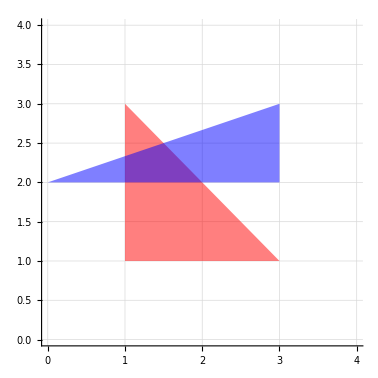

```mathematica
R=RegionIntersection[Triangle[tr1Points],Triangle[tr2Points]];
Graphics[{Red,Opacity[0.5],Triangle[tr1Points],Blue,Triangle[tr2Points]}, Axes->True,PlotRange->{{0, 4}, {0, 4}},GridLines->Automatic]
```

```mathematica
Area[R]
```

1/4